```mathematica
r = 10
d = 150
eq1 = y==x+(Sqrt[2]/2)*d
eq2 = y == -x-l/2-(Sqrt[2]/2)*w+Sqrt[2]*r
```

10

150

y==75 √2+x

y==10 √2-l/2-w/(√2)-x

```mathematica
Solve[eq1 && eq2, {x,y}]
```

{{x→1/4 (-130 √2-l-√2 w),y→1/4 (170 √2-l-√2 w)}}

```mathematica
p1={-l/2-(Sqrt[2]/2)*w+(Sqrt[2]/2)*r,(Sqrt[2]/2)*r}
p2={1/4 (-130 √2-l-√2 w),1/4 (170 √2-l-√2 w)}
```

{5 √2-l/2-w/(√2),5 √2}

{1/4 (-130 √2-l-√2 w),1/4 (170 √2-l-√2 w)}

```mathematica
n1 = Norm[p2-p1] > 10
```

√(Abs[-5 √2+l/2+w/(√2)+1/4 (-130 √2-l-√2 w)]^2+Abs[-5 √2+1/4 (170 √2-l-√2 w)]^2)>10

```mathematica
n2 = l/2+(Sqrt[2]/2)*w-(Sqrt[2]/2)*d<0
```

-75 √2+l/2+w/(√2)<0

```mathematica
n3=l-Sqrt[2]*w+2*Sqrt[2]*r-2*r > 10
```

-20+20 √2+l-√2 w>10

```mathematica
sol=Reduce[n1 && n2 && n3 && w>20 && l>0]
```

(30<l≤-10 √2+5 (3+13 √2)&&20<w<(-30+20 √2+l)/(√2))||(-10 √2+5 (3+13 √2)<l<110 √2&&20<w<-20+1/2 (300-√2 l))

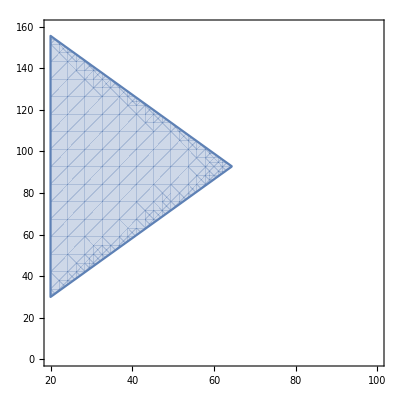

```mathematica
RegionPlot[sol,{w,20,100},{l,0,160}]
```

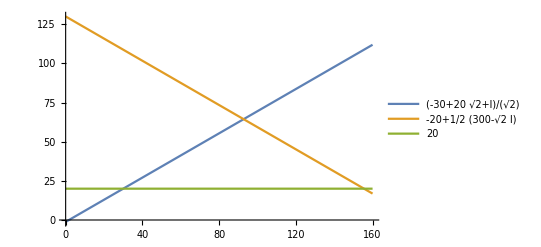

```mathematica
Plot[{(-30+20 √2+l)/(√2),-20+1/2 (300-√2 l),20},{l,0,160},PlotLegends->"Expressions"]
```

```mathematica
Solve[(-30+20 √2+l)/(√2)==-20+1/2 (300-√2 l),l]
```

```mathematica
{{l->(5 (22+3 √2))/(√2)}}//Simplify
```

{{l→15+55 √2}}

```mathematica
(-30+20 √2+l)/(√2)/.l->15+55 √2//Simplify
```

75-15/(√2)

```mathematica
p1 = {15+55 √2,75-15/(√2)}
p2={30,20}
p3 = {110 √2,20}
```

```mathematica
Solve[(-30+20 √2+l)/(√2)==20,l]
```

{{l→30}}

```mathematica
Solve[-20+1/2 (300-√2 l)==20,l]
```

{{l→110 √2}}